```mathematica
Clear["Global`*"]
```

定义矩阵

```mathematica
h=({{0, 0, 0, 0, 0, 0, 1, -ⅇ^(-ⅈ kx), 1/2, -1/2 ⅇ^(-ⅈ (kx/2-(√3 ky)/2)), 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, -(√3)/2, 1/2 √3 ⅇ^(-ⅈ (kx/2-(√3 ky)/2)), 0, 0}, {0, 0, 0, 0, 0, 0, -ⅇ^(-ⅈ kx), 1, 0, 0, 1/2, -1/2 ⅇ^(-ⅈ (kx/2+(√3 ky)/2))}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, (√3)/2, -1/2 √3 ⅇ^(-ⅈ (kx/2+(√3 ky)/2))}, {0, 0, 0, 0, 0, 0, 0, 0, -1/2 ⅇ^(-ⅈ (kx/2-(√3 ky)/2)), 1/2, -1/2 ⅇ^(-ⅈ (kx/2+(√3 ky)/2)), 1/2}, {0, 0, 0, 0, 0, 0, 0, 0, 1/2 √3 ⅇ^(-ⅈ (kx/2-(√3 ky)/2)), -(√3)/2, -1/2 √3 ⅇ^(-ⅈ (kx/2+(√3 ky)/2)), (√3)/2}, {1, 0, -ⅇ^(ⅈ kx), 0, 0, 0, 0, 0, 0, 0, 0, 0}, {-ⅇ^(ⅈ kx), 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1/2, -(√3)/2, 0, 0, -1/2 ⅇ^(1/2 ⅈ (kx-√3 ky)), 1/2 √3 ⅇ^(1/2 ⅈ (kx-√3 ky)), 0, 0, 0, 0, 0, 0}, {-1/2 ⅇ^(1/2 ⅈ (kx-√3 ky)), 1/2 √3 ⅇ^(1/2 ⅈ (kx-√3 ky)), 0, 0, 1/2, -(√3)/2, 0, 0, 0, 0, 0, 0}, {0, 0, 1/2, (√3)/2, -1/2 ⅇ^(1/2 ⅈ (kx+√3 ky)), -1/2 √3 ⅇ^(1/2 ⅈ (kx+√3 ky)), 0, 0, 0, 0, 0, 0}, {0, 0, -1/2 ⅇ^(1/2 ⅈ (kx+√3 ky)), -1/2 √3 ⅇ^(1/2 ⅈ (kx+√3 ky)), 1/2, (√3)/2, 0, 0, 0, 0, 0, 0}})
```

{{0,0,0,0,0,0,1,-ⅇ^(-ⅈ kx),1/2,-1/2 ⅇ^(-ⅈ (kx/2-(√3 ky)/2)),0,0},{0,0,0,0,0,0,0,0,-(√3)/2,1/2 √3 ⅇ^(-ⅈ (kx/2-(√3 ky)/2)),0,0},{0,0,0,0,0,0,-ⅇ^(-ⅈ kx),1,0,0,1/2,-1/2 ⅇ^(-ⅈ (kx/2+(√3 ky)/2))},{0,0,0,0,0,0,0,0,0,0,(√3)/2,-1/2 √3 ⅇ^(-ⅈ (kx/2+(√3 ky)/2))},{0,0,0,0,0,0,0,0,-1/2 ⅇ^(-ⅈ (kx/2-(√3 ky)/2)),1/2,-1/2 ⅇ^(-ⅈ (kx/2+(√3 ky)/2)),1/2},{0,0,0,0,0,0,0,0,1/2 √3 ⅇ^(-ⅈ (kx/2-(√3 ky)/2)),-(√3)/2,-1/2 √3 ⅇ^(-ⅈ (kx/2+(√3 ky)/2)),(√3)/2},{1,0,-ⅇ^(ⅈ kx),0,0,0,0,0,0,0,0,0},{-ⅇ^(ⅈ kx),0,1,0,0,0,0,0,0,0,0,0},{1/2,-(√3)/2,0,0,-1/2 ⅇ^(1/2 ⅈ (kx-√3 ky)),1/2 √3 ⅇ^(1/2 ⅈ (kx-√3 ky)),0,0,0,0,0,0},{-1/2 ⅇ^(1/2 ⅈ (kx-√3 ky)),1/2 √3 ⅇ^(1/2 ⅈ (kx-√3 ky)),0,0,1/2,-(√3)/2,0,0,0,0,0,0},{0,0,1/2,(√3)/2,-1/2 ⅇ^(1/2 ⅈ (kx+√3 ky)),-1/2 √3 ⅇ^(1/2 ⅈ (kx+√3 ky)),0,0,0,0,0,0},{0,0,-1/2 ⅇ^(1/2 ⅈ (kx+√3 ky)),-1/2 √3 ⅇ^(1/2 ⅈ (kx+√3 ky)),1/2,(√3)/2,0,0,0,0,0,0}}

坐标表格

```mathematica
sl=0.05;
```

```mathematica
kst=Table[{x,y},{x,-1.Pi,1.Pi,sl},{y,-1.Pi,1.Pi,sl}];
```

偏导数矩阵表格

```mathematica
htkx=Table[D[h,kx]/.{kx->x,ky->y},{x,-1.Pi,1.Pi,sl},{y,-1.Pi,1.Pi,sl}]//Parallelize;
```

```mathematica
htky=Table[D[h,ky]/.{kx->x,ky->y},{x,-1.Pi,1.Pi,sl},{y,-1.Pi,1.Pi,sl}]//Parallelize;
```

特征值特征向量表格

```mathematica
uneva=Table[N[Eigenvalues[h/.{kx->x,ky->y}]],{x,-1.Pi,1.Pi,sl},{y,-1.Pi,1.Pi,sl}]//Parallelize;
```

```mathematica
uneve=Table[N[Eigenvectors[h/.{kx->x,ky->y}]],{x,-1.Pi,1.Pi,sl},{y,-1.Pi,1.Pi,sl}]//Parallelize;
```

```mathematica
asso=MapThread[f,{uneva,uneve},2]/.{f->AssociationThread};
```

```mathematica
sorted=Map[Sort[#,Re[#1]<Re[#2]&]&,asso,2];
```

```mathematica
sorted[[1,1]]//Keys
```

{2.23616,-2.23616,1.73205,-1.73205,-1.5047,1.5047,0.999799,-0.999799,0.857838,-0.857838,-9.1609×10^-16,-4.16177×10^-16}

```mathematica
eva=Map[Keys,sorted];
```

```mathematica
eve=Map[Values,sorted];
```

曲率

```mathematica
bc[n_]:=-2*Table[Im[Sum[If[n≠n2,(Conjugate[eve[[nx,ny,n]]].htkx[[nx,ny]].eve[[nx,ny,n2]]*Conjugate[eve[[nx,ny,n2]]].htky[[nx,ny]].eve[[nx,ny,n]]/(eva[[nx,ny,n]]-eva[[nx,ny,n2]])^2),0],{n2,Dimensions[h][[1]]}]],{nx,1,Round[2Pi/sl]},{ny,1,Round[2Pi/sl]}];
```

作图

```mathematica
bct[n_]:=Module[{kk=bc[n]},Table[Flatten[{kst[[nx,ny]],kk[[nx,ny]]}],{nx,1,Round[2Pi/sl]},{ny,1,Round[2Pi/sl]}]];
```

```mathematica
Table[ListPlot3D[Flatten[bct[n],{1,2}]],{n,1,Dimensions[h][[1]]}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

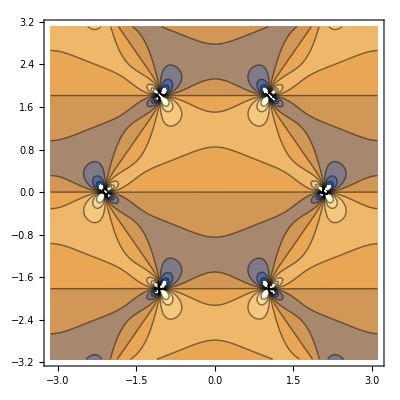
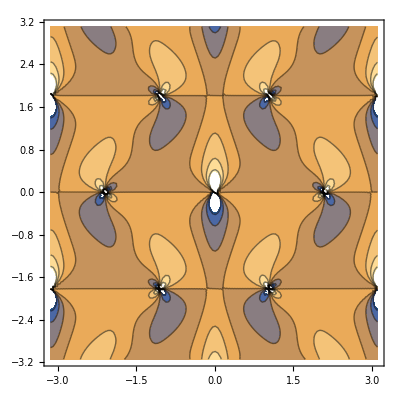
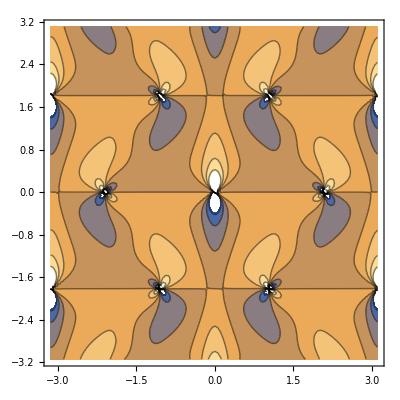
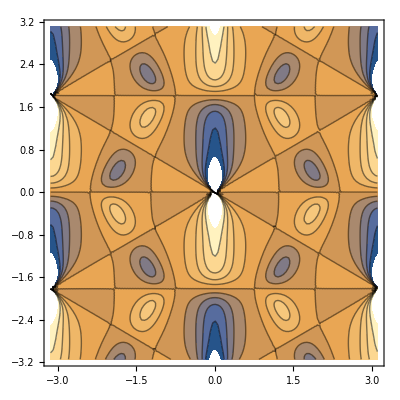
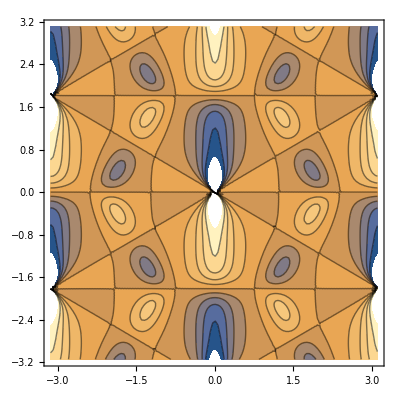
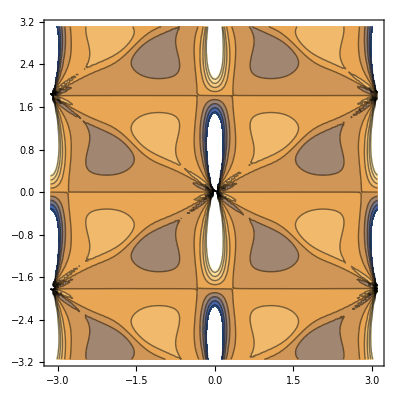
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ListContourPlot[Flatten[bct[n],{1,2}]],{n,1,Dimensions[h][[1]]}]
```

计算贝里相位

```mathematica
bf[n_]:=Module[{kk=bc[n]},Sum[sl^2*bc[n][[nx,ny]],{nx,1,Round[2Pi/sl]},{ny,1,Round[2Pi/sl]}]];
```

```mathematica
bf[1]
```

$Aborted